```mathematica
(* prompt U235 fission spectrum *)
Nrm=986229*1.00666; (* normalized to 1 between 0.1 and 10 MeV *)
s235U[en_]:=If[en>64700 && en<10*10^6,0.453*Exp[-1.036*en/10^6]*Sinh[Sqrt[2.29*en/10^6]]/Nrm,0];
Integrate[s235U[x],{x,64700,10*10^6}]
```

0.999995

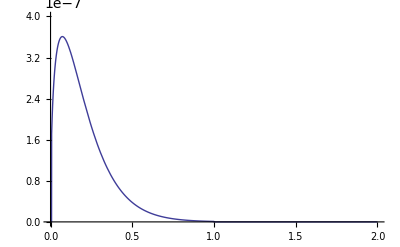

```mathematica
Plot[s235U[x],{x,0.000001,2*10^7},PlotRange->{0,4*10^-7}]
```

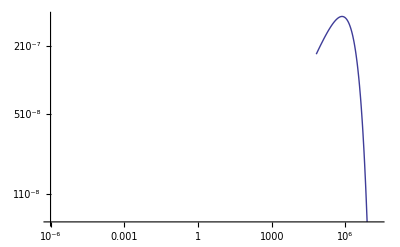

```mathematica
LogLogPlot[s235U[x],{x,0.000001,2*10^7}]
```

1.

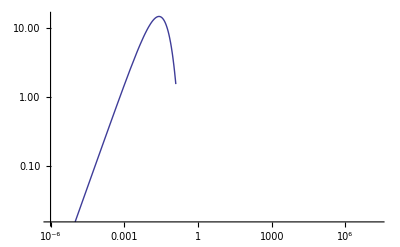

```mathematica
(* Maxwell Boltzmann Spectrum *)
Mrm=84481.8/0.674374; (* normalized to 1 between 0.00001 and 0.625 eV *)
k=8.6173324*10^-5;
T=300;
m=939.565378*10^6;
MB[en_]:=If[en>0.00001 && en<0.125,Mrm*2*Pi/((Pi*k*T)^1.5)*Sqrt[(2/m)]*en*Exp[-en/(k*T)],0];
Integrate[MB[x],{x,0.000001,10}] 
LogLogPlot[MB[x],{x,0.000001,2*10^7}]
```

```mathematica
FindMaximum[MB[x],{x,0.000011}] (*Maximum of reactor thermal power spectrum at 0.051 eV*)
```

{14.922,{x→0.025852}}

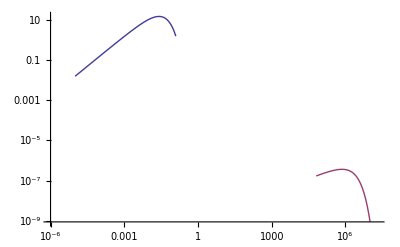

```mathematica
LogLogPlot[{MB[x],s235U[x]},{x,0.000001,2*10^7}]
```

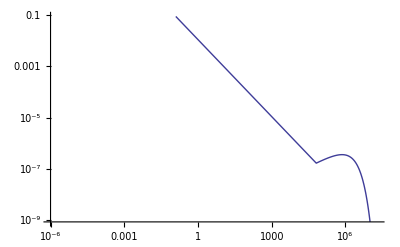

```mathematica
(* now comes the 1/E spectrum between the thermal and the fast group *)
ns1=s235U[64700.00001]*64700;
PhiFast[en_]:=If[en>64700 && en<10*10^6,s235U[en],If[en<64700&& en>0.125,ns1/en,0]];

LogLogPlot[PhiFast[x],{x,0.000001,2*10^7}]
```

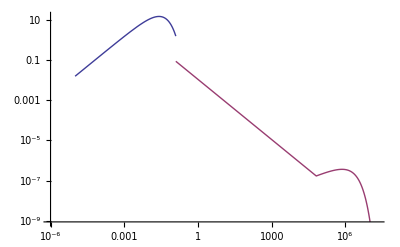

```mathematica
LogLogPlot[{MB[x],PhiFast[x]},{x,0.000001,2*10^7}]
```

```mathematica
SigmaFission=0.185;SigmaTotal=0.012;
(* normalize fission spectrum *)
NIntegrate[SigmaFission*PhiFast[x]/SigmaTotal,{x,0.625,10*10^6}]
```

17.3555

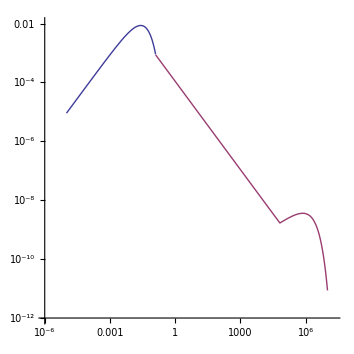

```mathematica
norm=100;
LogLogPlot[{(MB[x]/17.3)/norm,PhiFast[x]/norm},{x,0.000001,2*10^7},PlotRange->{10^-12,0.01},AspectRatio->1]
```